```mathematica
从P倒推需要的Mdot
假设现在源处于spin equilibrium，又现在的周期P推出此时的Mdot，并由此倒推初始盘的质量和回落盘形成时间;
P1=1.427579,Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403,Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316,Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042,Pdot4=-4.7*^-9;MJD4=56851.5;
MJD in units of day;
```

```mathematica
case1,取Mdot为常数
```

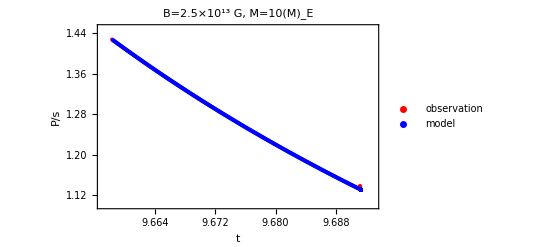

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.946*10^18;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

Mdot=10*MdotEdd;
B=2.5*10^13;

mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);

P1=1.427579;Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
day=24*3600.;
t1=MJD1*day;
t2=MJD2*day;
t3=MJD3*day;
t4=MJD4*day;
dataPobs={{Log[10,t1],P1},{Log[10,t2],P2},{Log[10,t3],P3},{Log[10,t4],P4}};

P=P1;
t=MJD1*24*3600.;
MJD4=56851.5*24*3600.;

dataP=Table[
n;
torque=Mdot*(G*M*Rin)^(1/2);
Pdot=-(torque*P^2.)/(2.*Pi*10^45.);
dt=If[t<MJD4,Min[10^-3*P/Abs[Pdot],10^-3*t],0];
t=t+dt;
P=P+Pdot*dt;
(*t=t/(24*3600.);*)
{Log[10,t],P},
{n,1,1000}];

ListPlot[{dataPobs,dataP},Frame->True,PlotRange->{{9.657,9.693},{1.1,1.45}},PlotLabel->"B=2.5×10^13 G, Ṁ=10(Ṁ)_E",FrameLabel->{"t","P/s"},PlotLegends->Placed[{"observation","model"},{0.8,0.8}],PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Small]}}]
```

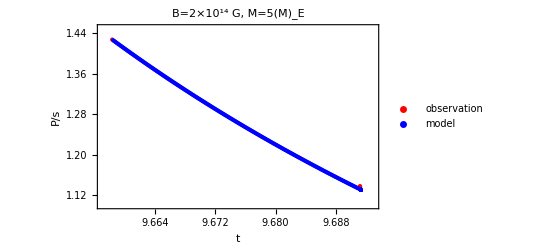

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.946*10^18;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

Mdot=5*MdotEdd;
B=2.0*10^14;

mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);

P1=1.427579;Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
day=24*3600.;
t1=MJD1*day;
t2=MJD2*day;
t3=MJD3*day;
t4=MJD4*day;
dataPobs={{Log[10,t1],P1},{Log[10,t2],P2},{Log[10,t3],P3},{Log[10,t4],P4}};

P=P1;
t=MJD1*24*3600.;
MJD4=56851.5*24*3600.;

dataP=Table[
n;
torque=Mdot*(G*M*Rin)^(1/2);
Pdot=-(torque*P^2.)/(2.*Pi*10^45.);
dt=If[t<MJD4,Min[10^-3*P/Abs[Pdot],10^-3*t],0];
t=t+dt;
P=P+Pdot*dt;
(*t=t/(24*3600.);*)
{Log[10,t],P},
{n,1,1000}];

ListPlot[{dataPobs,dataP},Frame->True,PlotRange->{{9.657,9.693},{1.1,1.45}},PlotLabel->"B=2×10^14 G, Ṁ=5(Ṁ)_E",FrameLabel->{"t","P/s"},PlotLegends->Placed[{"observation","model"},{0.8,0.8}],PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Small]}}]
```

```mathematica
ListLinePlot[{dataP,dataPobs},Frame->True,PlotRange->{{9.657,9.693},{1.1,1.45}}]
```

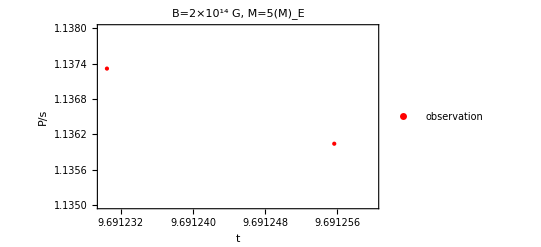

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.946*10^18;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

Mdot=5*MdotEdd;
B=2.0*10^14;

mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);

P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
day=24*3600.;
t2=MJD2*day;
t3=MJD3*day;
t4=MJD4*day;
dataPobs={{Log[10,t2],P2},{Log[10,t3],P3},{Log[10,t4],P4}};


ListPlot[{dataPobs},Frame->True,PlotRange->{{9.69123,9.69126},{1.135,1.138}},PlotLabel->"B=2×10^14 G, Ṁ=5(Ṁ)_E",FrameLabel->{"t","P/s"},PlotLegends->Placed[{"observation","model"},{0.8,0.8}],PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Small]}}]
```

```mathematica
dataPobs
```

{{9.69123,1.1374},{9.69123,1.13732},{9.69126,1.13604}}

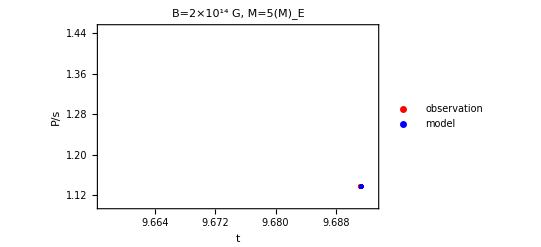

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.946*10^18;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

Mdot=5*MdotEdd;
B=2.0*10^14;

mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);

P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
day=24*3600.;
t2=MJD2*day;
t3=MJD3*day;
t4=MJD4*day;
dataPobs={{Log[10,t2],P2},{Log[10,t3],P3},{Log[10,t4],P4}};

P=P2;
t=MJD2*24*3600.;
MJD4=56851.5*24*3600.;

dataP=Table[
n;
torque=Mdot*(G*M*Rin)^(1/2);
Pdot=-(torque*P^2.)/(2.*Pi*10^45.);
dt=If[t<MJD4,Min[10^-3*P/Abs[Pdot],10^-3*t],0];
t=t+dt;
P=P+Pdot*dt;
(*t=t/(24*3600.);*)
{Log[10,t],P},
{n,1,1000}];

ListPlot[{dataPobs,dataP},Frame->True,PlotRange->{{9.657,9.693},{1.1,1.45}},PlotLabel->"B=2×10^14 G, Ṁ=5(Ṁ)_E",FrameLabel->{"t","P/s"},PlotLegends->Placed[{"observation","model"},{0.8,0.8}],PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Small]}}]
```